```mathematica
CalculateMathieuEnergies[n_,k_,q_] :=
	Module[{data},
data=Table[MathieuCharacteristicA[i,j]//N,{i,-1*k,k,2*k/(n-1)},{j,-1*q,q,2*q/(n-1)}];
Export["Mathieu_values.json",data,"ExpressionJSON"];]
```

```mathematica
CalculateMathieuEnergies[500,5,1.0*3.8589003840022436]
```

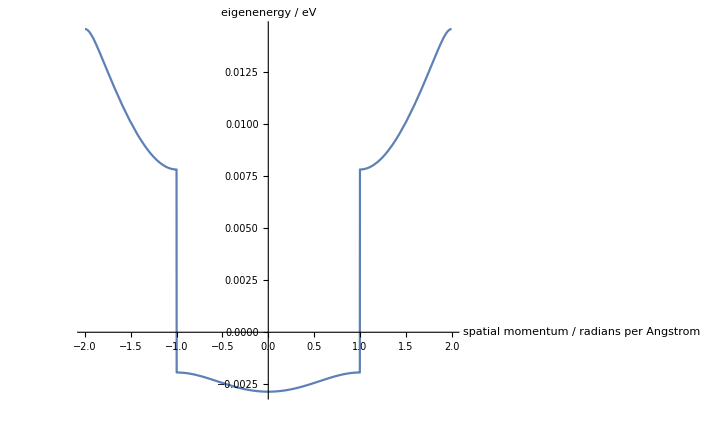

```mathematica
Plot[MathieuCharacteristicA[r,0.01*132.5520520861412]*π^2*(10^10/157.86353)^2*(6.626*10^-34)^2/2/2/π/π/2/(9.11*10^-31)/0.4/(1.60022*10^-19),{r,-2,2}, Axes-> True, AxesLabel->{"spatial momentum / radians per Angstrom","eigenenergy / eV"}]
```

```mathematica
CalculateMathieuFunctions[n_,emin_,emax_,q_,r_,k_] :=
	Module[{data},
data=Table[MathieuC[e,q,x*k*π]//N,{e,emin,emax,(emax-emin)/(n-1)},{x,-r/k,r/k,2*r/k/(n-1)}];
Export["Mathieu_functions.json",data,"ExpressionJSON"];]
```

```mathematica
CalculateMathieuFunctions[500,-0.25*3.8589003840022436*2,.75*132.5520520861412*2,0.25*132.5520520861412,2,0.037126125988993584]
```

```mathematica
Plot[MathieuC[-240,1.0*132.5520520861412,z*0.006334585321891637*π],{z,-2/0.006334585321891637,2/0.006334585321891637}]
```

-Graphics-

```mathematica
MathieuCharacteristicA[0,1.0*132.5520520861412]*π^2*(10^10/157.86353)^2*(6.626*10^-34)^2/2/2/π/π/2/(9.11*10^-31)/0.4/(1.60022*10^-19)
```

-0.915165